# 2 DEG Magneto - electric Properties

## Inverse scattering time matrix diagonal elements ( l=0)

#### Landau Level

```mathematica
(*M = 0; *)
```

#### Gauss-Hermite Function χ_N

```mathematica
χ[y_?NumericQ,N_?NumericQ]:= Exp[-y^2/2]/(√(2^N*N!*√π))HermiteH[N,y];
```

#### Landau Level N = 0

```mathematica
Q0:= χ[y2,0]*χ[y1-y2,0];
A0[y1_?NumericQ,E_?NumericQ]:=(BesselJ[0,E*(y1)])*NIntegrate[Q0,{y2,-Infinity,Infinity},AccuracyGoal->4];
Sup0 := NIntegrate[A0[y1,e]^2,{y1,-Infinity,Infinity},AccuracyGoal->4];
Sdown0:= NIntegrate[A0[y1,0]^2,{y1,-Infinity,Infinity},AccuracyGoal->4];
Tinverse0 := Sup0/Sdown0;
```

```mathematica
P0=Plot[Tinverse0 ,{e,0,10},PlotRange->{{0,10},{0,1.2}},PlotStyle->{LightBlue},AxesLabel->{Style["E",FontSize->15,FontColor->White],Style["Inverse Scattering Time",FontSize->15,FontColor->White]},
AxesStyle->{Directive[Black,15],Directive[Black,15]},LabelStyle->Larger,MaxRecursion->0,PlotPoints->50];
```

#### Landau Level N = 1

```mathematica
Q1:= χ[y2,1]*χ[y1-y2,1];
A1[y1_?NumericQ,E_?NumericQ]:=(BesselJ[0,E*(y1)])*NIntegrate[Q1,{y2,-Infinity,Infinity},AccuracyGoal->4];
Sup1:= NIntegrate[A1[y1,e]^2,{y1,-Infinity,Infinity},AccuracyGoal->4];
Sdown1:= NIntegrate[A1[y1,0]^2,{y1,-Infinity,Infinity},AccuracyGoal->4];
Tinverse1 := Sup1/Sdown1;
P1=Plot[Tinverse1 ,{e,0,10},PlotRange->{{0,10},{0,1.2}},PlotStyle->{LightRed},AxesLabel->{Style["E",FontSize->15,FontColor->White],Style["Inverse Scattering Time",FontSize->15,FontColor->White]},
AxesStyle->{Directive[Black,15],Directive[Black,15]},LabelStyle->Larger,MaxRecursion->0,PlotPoints->50];
```

#### Landau Level N = 2

```mathematica
Q2:= χ[y2,2]*χ[y1-y2,2];
A2[y1_?NumericQ,E_?NumericQ]:=(BesselJ[0,E*(y1)])*NIntegrate[Q2,{y2,-Infinity,Infinity},AccuracyGoal->4];
Sup2:= NIntegrate[A2[y1,e]^2,{y1,-Infinity,Infinity},AccuracyGoal->4];
Sdown2:= NIntegrate[A2[y1,0]^2,{y1,-Infinity,Infinity},AccuracyGoal->4];
Tinverse2 := Sup2/Sdown2;
P2=Plot[Tinverse2 ,{e,0,10},PlotRange->{{0,10},{0,1.2}},PlotStyle->{LightGreen},AxesLabel->{Style["E",FontSize->15,FontColor->White],Style["Inverse Scattering Time",FontSize->15,FontColor->White]},
AxesStyle->{Directive[Black,15],Directive[Black,15]},LabelStyle->Larger,MaxRecursion->0,PlotPoints->50];
```

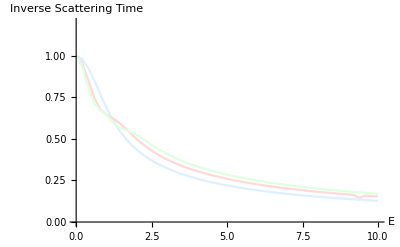

```mathematica
Show[P0,P1,P2]
```

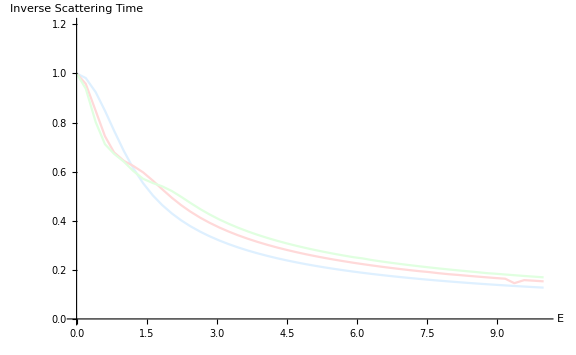

```mathematica
Show[%42,ImageSize->Large]
```